### Varying cell colour percentages --> interesting results

```mathematica
colornum = 3;
Quiet[Integer[colornum]^=True;]

RulPlt[rulenum_]:=RulePlot[CellularAutomaton[{rulenum,3}],ColorRules->{0->Yellow,1->Red,2->Blue},MeshStyle->Orange, ImageSize -> Large];

RuleLoop[rulenum_, peryell_, perred_, perblue_:0.1]:= BlockRandom[SeedRandom[1000];

ArrayPlot[CellularAutomaton[{rulenum, 3},RandomChoice[{peryell, perred, perblue}-> {0,1,2}, 120],30],Mesh->True,ColorRules->{0->Yellow,1->Red, 2-> Blue},MeshStyle->Orange, ImageSize ->  Large]];
```

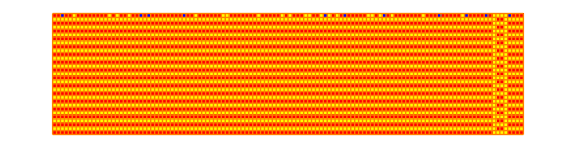
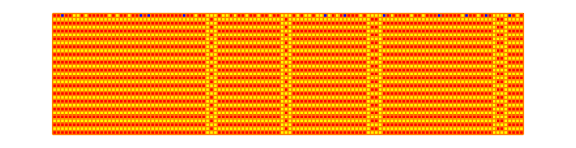
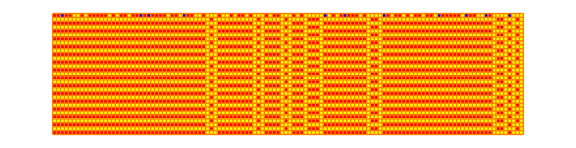
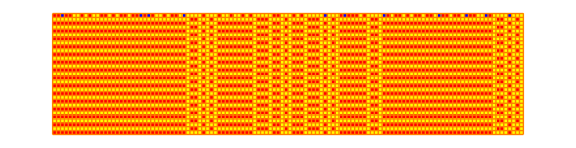
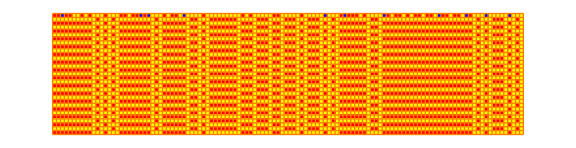
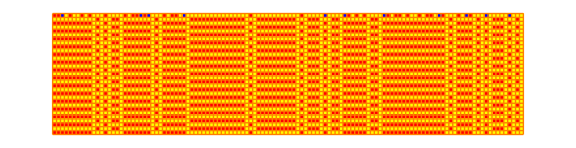
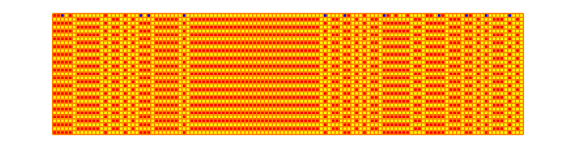
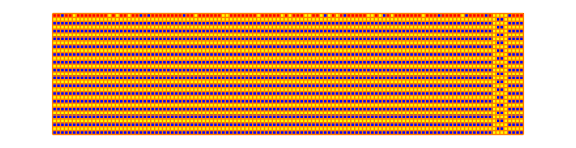
{-Graphics-,0.2,1} | {-Graphics-,0.3,1} | {-Graphics-,0.4,1} | {-Graphics-,0.5,1} | {-Graphics-,0.6,1} | {-Graphics-,0.7,1} | {-Graphics-,0.8,1}
{-Graphics-,0.2,2} | {-Graphics-,0.3,2} | {-Graphics-,0.4,2} | {-Graphics-,0.5,2} | {-Graphics-,0.6,2} | {-Graphics-,0.7,2} | {-Graphics-,0.8,2}
{-Graphics-,0.2,3} | {-Graphics-,0.3,3} | {-Graphics-,0.4,3} | {-Graphics-,0.5,3} | {-Graphics-,0.6,3} | {-Graphics-,0.7,3} | {-Graphics-,0.8,3}
{-Graphics-,0.2,4} | {-Graphics-,0.3,4} | {-Graphics-,0.4,4} | {-Graphics-,0.5,4} | {-Graphics-,0.6,4} | {-Graphics-,0.7,4} | {-Graphics-,0.8,4}
{-Graphics-,0.2,5} | {-Graphics-,0.3,5} | {-Graphics-,0.4,5} | {-Graphics-,0.5,5} | {-Graphics-,0.6,5} | {-Graphics-,0.7,5} | {-Graphics-,0.8,5}
{-Graphics-,0.2,6} | {-Graphics-,0.3,6} | {-Graphics-,0.4,6} | {-Graphics-,0.5,6} | {-Graphics-,0.6,6} | {-Graphics-,0.7,6} | {-Graphics-,0.8,6}
{-Graphics-,0.2,7} | {-Graphics-,0.3,7} | {-Graphics-,0.4,7} | {-Graphics-,0.5,7} | {-Graphics-,0.6,7} | {-Graphics-,0.7,7} | {-Graphics-,0.8,7}
{-Graphics-,0.2,8} | {-Graphics-,0.3,8} | {-Graphics-,0.4,8} | {-Graphics-,0.5,8} | {-Graphics-,0.6,8} | {-Graphics-,0.7,8} | {-Graphics-,0.8,8}
{-Graphics-,0.2,9} | {-Graphics-,0.3,9} | {-Graphics-,0.4,9} | {-Graphics-,0.5,9} | {-Graphics-,0.6,9} | {-Graphics-,0.7,9} | {-Graphics-,0.8,9}
{-Graphics-,0.2,10} | {-Graphics-,0.3,10} | {-Graphics-,0.4,10} | {-Graphics-,0.5,10} | {-Graphics-,0.6,10} | {-Graphics-,0.7,10} | {-Graphics-,0.8,10}

```mathematica
Grid[Table[{RuleLoop[rulenum, peryell, 1-peryell-0.1], peryell,rulenum},{rulenum, 10}, {peryell,0.2,0.8,0.1}]] (*Varying Yellow and Red* for rules 1 to 10*)
```

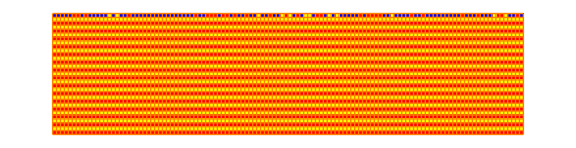
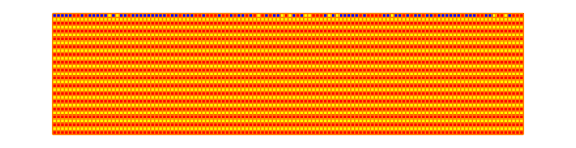
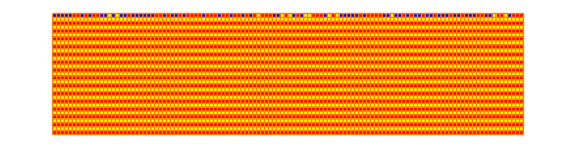
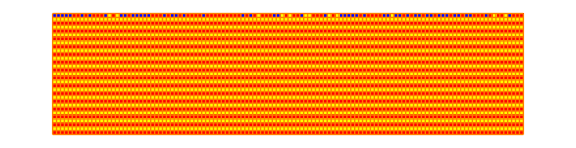
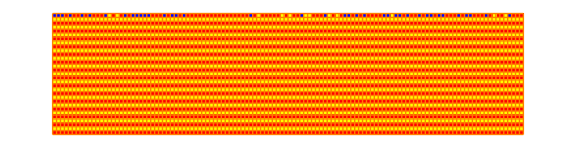
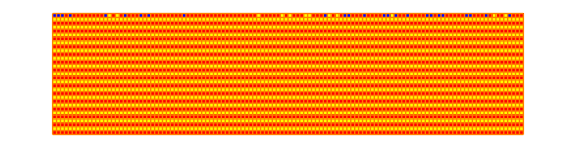
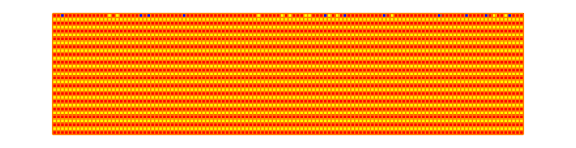
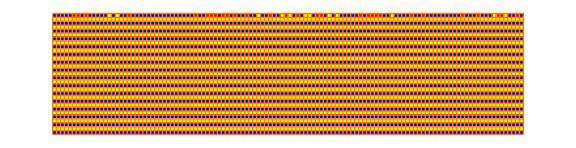
{-Graphics-,0.2,1} | {-Graphics-,0.3,1} | {-Graphics-,0.4,1} | {-Graphics-,0.5,1} | {-Graphics-,0.6,1} | {-Graphics-,0.7,1} | {-Graphics-,0.8,1}
{-Graphics-,0.2,2} | {-Graphics-,0.3,2} | {-Graphics-,0.4,2} | {-Graphics-,0.5,2} | {-Graphics-,0.6,2} | {-Graphics-,0.7,2} | {-Graphics-,0.8,2}
{-Graphics-,0.2,3} | {-Graphics-,0.3,3} | {-Graphics-,0.4,3} | {-Graphics-,0.5,3} | {-Graphics-,0.6,3} | {-Graphics-,0.7,3} | {-Graphics-,0.8,3}
{-Graphics-,0.2,4} | {-Graphics-,0.3,4} | {-Graphics-,0.4,4} | {-Graphics-,0.5,4} | {-Graphics-,0.6,4} | {-Graphics-,0.7,4} | {-Graphics-,0.8,4}
{-Graphics-,0.2,5} | {-Graphics-,0.3,5} | {-Graphics-,0.4,5} | {-Graphics-,0.5,5} | {-Graphics-,0.6,5} | {-Graphics-,0.7,5} | {-Graphics-,0.8,5}
{-Graphics-,0.2,6} | {-Graphics-,0.3,6} | {-Graphics-,0.4,6} | {-Graphics-,0.5,6} | {-Graphics-,0.6,6} | {-Graphics-,0.7,6} | {-Graphics-,0.8,6}
{-Graphics-,0.2,7} | {-Graphics-,0.3,7} | {-Graphics-,0.4,7} | {-Graphics-,0.5,7} | {-Graphics-,0.6,7} | {-Graphics-,0.7,7} | {-Graphics-,0.8,7}
{-Graphics-,0.2,8} | {-Graphics-,0.3,8} | {-Graphics-,0.4,8} | {-Graphics-,0.5,8} | {-Graphics-,0.6,8} | {-Graphics-,0.7,8} | {-Graphics-,0.8,8}
{-Graphics-,0.2,9} | {-Graphics-,0.3,9} | {-Graphics-,0.4,9} | {-Graphics-,0.5,9} | {-Graphics-,0.6,9} | {-Graphics-,0.7,9} | {-Graphics-,0.8,9}
{-Graphics-,0.2,10} | {-Graphics-,0.3,10} | {-Graphics-,0.4,10} | {-Graphics-,0.5,10} | {-Graphics-,0.6,10} | {-Graphics-,0.7,10} | {-Graphics-,0.8,10}

```mathematica
Grid[Table[{RuleLoop[rulenum,0.1 , perred, 1-0.1-perred], perred,rulenum},{rulenum, 10}, {perred,0.2,0.8,0.1}]] (*Varying Red and Blue* for rules 1 to 10*)
```

```mathematica
Grid[Table[{RuleLoop[rulenum, peryell,0.1,1- peryell- 0.1], peryell,rulenum},{rulenum, 10}, {peryell,0.2,0.8,0.1}]] (*Varying Yellow and Blue* for rules 1 to 10*)
```

{-Graphics-,0.2,1} | {-Graphics-,0.3,1} | {-Graphics-,0.4,1} | {-Graphics-,0.5,1} | {-Graphics-,0.6,1} | {-Graphics-,0.7,1} | {-Graphics-,0.8,1}
{-Graphics-,0.2,2} | {-Graphics-,0.3,2} | {-Graphics-,0.4,2} | {-Graphics-,0.5,2} | {-Graphics-,0.6,2} | {-Graphics-,0.7,2} | {-Graphics-,0.8,2}
{-Graphics-,0.2,3} | {-Graphics-,0.3,3} | {-Graphics-,0.4,3} | {-Graphics-,0.5,3} | {-Graphics-,0.6,3} | {-Graphics-,0.7,3} | {-Graphics-,0.8,3}
{-Graphics-,0.2,4} | {-Graphics-,0.3,4} | {-Graphics-,0.4,4} | {-Graphics-,0.5,4} | {-Graphics-,0.6,4} | {-Graphics-,0.7,4} | {-Graphics-,0.8,4}
{-Graphics-,0.2,5} | {-Graphics-,0.3,5} | {-Graphics-,0.4,5} | {-Graphics-,0.5,5} | {-Graphics-,0.6,5} | {-Graphics-,0.7,5} | {-Graphics-,0.8,5}
{-Graphics-,0.2,6} | {-Graphics-,0.3,6} | {-Graphics-,0.4,6} | {-Graphics-,0.5,6} | {-Graphics-,0.6,6} | {-Graphics-,0.7,6} | {-Graphics-,0.8,6}
{-Graphics-,0.2,7} | {-Graphics-,0.3,7} | {-Graphics-,0.4,7} | {-Graphics-,0.5,7} | {-Graphics-,0.6,7} | {-Graphics-,0.7,7} | {-Graphics-,0.8,7}
{-Graphics-,0.2,8} | {-Graphics-,0.3,8} | {-Graphics-,0.4,8} | {-Graphics-,0.5,8} | {-Graphics-,0.6,8} | {-Graphics-,0.7,8} | {-Graphics-,0.8,8}
{-Graphics-,0.2,9} | {-Graphics-,0.3,9} | {-Graphics-,0.4,9} | {-Graphics-,0.5,9} | {-Graphics-,0.6,9} | {-Graphics-,0.7,9} | {-Graphics-,0.8,9}
{-Graphics-,0.2,10} | {-Graphics-,0.3,10} | {-Graphics-,0.4,10} | {-Graphics-,0.5,10} | {-Graphics-,0.6,10} | {-Graphics-,0.7,10} | {-Graphics-,0.8,10}

```mathematica
Grid[Table[{RuleLoop[rulenum,0.,perred,1-perred],perred,rulenum},{rulenum, 10}, {perred,0.,1.0,0.1}]] (*Varying Red & Blue for rules 1 to 10*)
```

{-Graphics-,0.,1} | {-Graphics-,0.1,1} | {-Graphics-,0.2,1} | {-Graphics-,0.3,1} | {-Graphics-,0.4,1} | {-Graphics-,0.5,1} | {-Graphics-,0.6,1} | {-Graphics-,0.7,1} | {-Graphics-,0.8,1} | {-Graphics-,0.9,1} | {-Graphics-,1.,1}
{-Graphics-,0.,2} | {-Graphics-,0.1,2} | {-Graphics-,0.2,2} | {-Graphics-,0.3,2} | {-Graphics-,0.4,2} | {-Graphics-,0.5,2} | {-Graphics-,0.6,2} | {-Graphics-,0.7,2} | {-Graphics-,0.8,2} | {-Graphics-,0.9,2} | {-Graphics-,1.,2}
{-Graphics-,0.,3} | {-Graphics-,0.1,3} | {-Graphics-,0.2,3} | {-Graphics-,0.3,3} | {-Graphics-,0.4,3} | {-Graphics-,0.5,3} | {-Graphics-,0.6,3} | {-Graphics-,0.7,3} | {-Graphics-,0.8,3} | {-Graphics-,0.9,3} | {-Graphics-,1.,3}
{-Graphics-,0.,4} | {-Graphics-,0.1,4} | {-Graphics-,0.2,4} | {-Graphics-,0.3,4} | {-Graphics-,0.4,4} | {-Graphics-,0.5,4} | {-Graphics-,0.6,4} | {-Graphics-,0.7,4} | {-Graphics-,0.8,4} | {-Graphics-,0.9,4} | {-Graphics-,1.,4}
{-Graphics-,0.,5} | {-Graphics-,0.1,5} | {-Graphics-,0.2,5} | {-Graphics-,0.3,5} | {-Graphics-,0.4,5} | {-Graphics-,0.5,5} | {-Graphics-,0.6,5} | {-Graphics-,0.7,5} | {-Graphics-,0.8,5} | {-Graphics-,0.9,5} | {-Graphics-,1.,5}
{-Graphics-,0.,6} | {-Graphics-,0.1,6} | {-Graphics-,0.2,6} | {-Graphics-,0.3,6} | {-Graphics-,0.4,6} | {-Graphics-,0.5,6} | {-Graphics-,0.6,6} | {-Graphics-,0.7,6} | {-Graphics-,0.8,6} | {-Graphics-,0.9,6} | {-Graphics-,1.,6}
{-Graphics-,0.,7} | {-Graphics-,0.1,7} | {-Graphics-,0.2,7} | {-Graphics-,0.3,7} | {-Graphics-,0.4,7} | {-Graphics-,0.5,7} | {-Graphics-,0.6,7} | {-Graphics-,0.7,7} | {-Graphics-,0.8,7} | {-Graphics-,0.9,7} | {-Graphics-,1.,7}
{-Graphics-,0.,8} | {-Graphics-,0.1,8} | {-Graphics-,0.2,8} | {-Graphics-,0.3,8} | {-Graphics-,0.4,8} | {-Graphics-,0.5,8} | {-Graphics-,0.6,8} | {-Graphics-,0.7,8} | {-Graphics-,0.8,8} | {-Graphics-,0.9,8} | {-Graphics-,1.,8}
{-Graphics-,0.,9} | {-Graphics-,0.1,9} | {-Graphics-,0.2,9} | {-Graphics-,0.3,9} | {-Graphics-,0.4,9} | {-Graphics-,0.5,9} | {-Graphics-,0.6,9} | {-Graphics-,0.7,9} | {-Graphics-,0.8,9} | {-Graphics-,0.9,9} | {-Graphics-,1.,9}
{-Graphics-,0.,10} | {-Graphics-,0.1,10} | {-Graphics-,0.2,10} | {-Graphics-,0.3,10} | {-Graphics-,0.4,10} | {-Graphics-,0.5,10} | {-Graphics-,0.6,10} | {-Graphics-,0.7,10} | {-Graphics-,0.8,10} | {-Graphics-,0.9,10} | {-Graphics-,1.,10}